```mathematica
Normalize[{1, f'[x]}].Normalize[{a-x,b-f[x]}]
```

(a-x)/(√(Abs[a-x]^2+Abs[b-f[x]]^2) √(1+Abs[f'[x]]^2))+((b-f[x]) f'[x])/(√(Abs[a-x]^2+Abs[b-f[x]]^2) √(1+Abs[f'[x]]^2))

```mathematica
With[{f=#1^2&},
Normalize[{1, f'[x]}].Normalize[{a-x,b-f[x]}]]
```

(a-x)/(√(1+4 Abs[x]^2) √(Abs[a-x]^2+Abs[b-x^2]^2))+(2 x (b-x^2))/(√(1+4 Abs[x]^2) √(Abs[a-x]^2+Abs[b-x^2]^2))

```mathematica
Manipulate[
With[{f=#1^2&},
Normalize[{1, f'[x]}].Normalize[{a-x,b-f[x]}]],
{a, -1, 1}, {b, -1, 1}]
```

```mathematica
Manipulate[
With[{f=#1^2&},
Plot[Normalize[{1, f'[x]}].Normalize[{a-x,b-f[x]}], {x, -2, 2}]],
{a, -1, 1}, {b, -1, 1}]
```

```mathematica
{x-Sin[x], x+Sin[x]}
```

{x-Sin[x],x+Sin[x]}

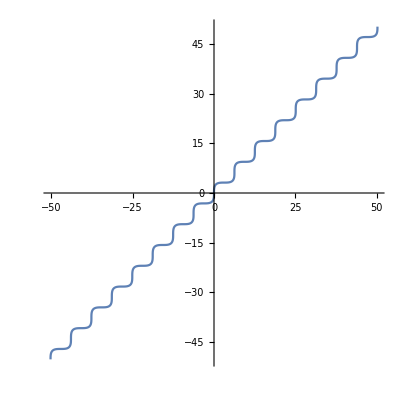

```mathematica
ParametricPlot[{x-Sin[x],x+Sin[x]},{x,-16 π,16 π}]
```

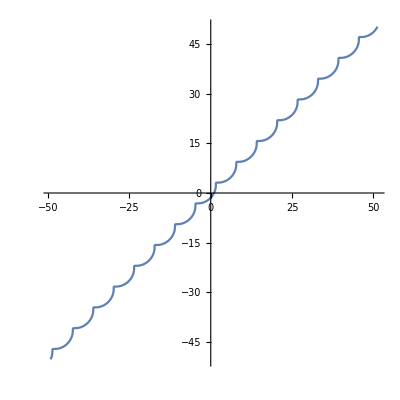

```mathematica
ParametricPlot[{x+Cos[x],x+Sin[x]},{x,-16 π,16 π}]
```

```mathematica
ParametricPlot[{x-Sin[x],x+Sin[x]},{x,-16 π,16 π}]
```

-Graphics-

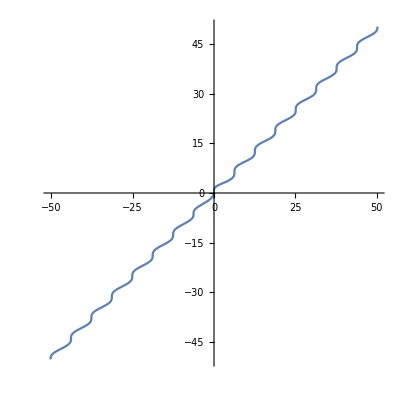

```mathematica
ParametricPlot[{x-Sin[x],x+Sin[x]/(2x)},{x,-16 π,16 π}]
```

```mathematica
{x, f[x]}+{1, -f'[x]}
```

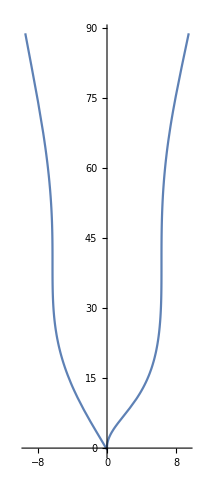

```mathematica
ParametricPlot[{x-Sin[x],x^2+Sin[x]},{x,-3π,3 π}]
```